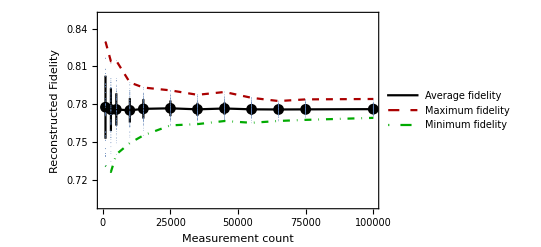

MeasurementConverge.pdf

```mathematica
Needs["ErrorBarPlots`"]

Xcord={1000,3000,5000,10000,15000,25000,35000,45000,55000,65000,75000,100000};
Length[Xcord];
Zcord={0.77764171,0.77574068,0.77586194,0.77514518,0.77633104,0.77676798,0.77595279,0.7766145,0.77595946,0.77583626,0.77592579,0.77610106};
Length[Zcord];
ZcordMax={0.829739,0.814078,0.814537,0.797296 ,0.793281,0.791021,0.787493 ,0.789728,0.785107,0.782536,0.783858,0.784171};
ZcordMin={0.731005,0.726222,0.740227,0.749174,0.755248,0.763217 ,0.76421 ,0.766676,0.765256,0.766726,0.767582,0.769179};

FaveSTD={0.025037456,0.017021549,0.012822759,0.009677274,0.007716961,0.006223711,0.005201828,0.004873395,0.004082144,0.003269443,0.003399914,0.002922127};
FaveErr=Transpose[{Xcord,Zcord,FaveSTD}];
Fave=Transpose[{Xcord,Zcord}];
Fmax=Transpose[{Xcord,ZcordMax}];
Fmin=Transpose[{Xcord,ZcordMin}];
LineAve = ListLinePlot[Fave,PlotRange->{0.7,0.85},PlotStyle->{Darker[Black]},PlotLegends->{"Average fidelity"}];
LineMax = ListLinePlot[Fmax,PlotRange->{0.7,0.85},PlotStyle->{Darker[Red],Dashed},PlotLegends->{"Maximum fidelity"}];
LineMin = ListLinePlot[Fmin,PlotRange->{0.7,0.85},PlotStyle->{Darker[Green],DotDashed},PlotLegends->{"Minimum fidelity"}];
LineAveErr=ErrorListPlot[FaveErr,PlotRange->{0.7,0.85},PlotStyle->Darker[Black]];

FT={.797030,.7715190,.7840210,.7948510,.7760140,.7747640,.7925740,.7518410,.7558910,.7831660,.7718650,.7973670,.7874560,.77450,.7585780,.7664030,.7749020,.7494330,.7650610,.7784460,.7824120,.7932540,.7734960,.7493670,.7641510,.7882750,.813910,.7822770,.7582870,.7672020,.7934480,.7764060,.7739620,.7644110,.7894040,.7425050,.7718850,.7952450,.7548460,.7537140,.7775890,.7913080,.7871110,.7659720,.778890,.7698580,.7534450,.7717160,.7780930,.7576570,.8001650,.8004160,.8125420,.746230,.7898190,.73470,.7752460,.7681910,.7927130,.7646740,.7853250,.7536070,.784390,.7954250,.7988480,.7655170,.7755820,.7772270,.7679720,.7717690,.7595530,.7794190,.7635550,.77480,.7650850,.7670450,.7409130,.7860480,.7772870,.7976010,.7262220,.7806790,.7638120,.7589510,.7932950,.7649760,.7933430,.7755730,.7788480,.7854690,.7655130,.7932980,.7885340,.7974850,.79280,.7827840,.7880110,.7579540,.7750010,.814078};

ft3=Transpose[{ConstantArray[3000,100],FT}];
ft3=ListPlot[ft3,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.798875,0.771208,0.765901,0.814537,0.77995,0.760287,0.778325,0.749304,0.767267,0.76656,0.778958,0.780165,0.769085,0.77185,0.773871,0.772751,0.77643,0.776501,0.76336,0.79156,0.767292,0.78459,0.779269,0.75671,0.798731,0.790146,0.774601,0.774013,0.789861,0.751038,0.783843,0.771265,0.787601,0.766966,0.795184,0.768315,0.766097,0.78364,0.755646,0.764353,0.78698,0.777504,0.765559,0.783223,0.789886,0.783279,0.764806,0.784529,0.781081,0.764709,0.785282,0.776993,0.789862,0.762993,0.7942,0.774084,0.785988,0.779612,0.784108,0.792292,0.767453,0.760399,0.777872,0.776893,0.768572,0.790927,0.762131,0.762275,0.753139,0.7803,0.773439,0.772325,0.778397,0.763497,0.759906,0.753229,0.776958,0.784714,0.776441,0.784301,0.75827,0.763363,0.774005,0.794461,0.774431,0.760595,0.781726,0.775088,0.782673,0.784236,0.787787,0.785667,0.764071,0.80056,0.798472,0.774872,0.740227,0.786506,0.785893,0.767247};
ft5=Transpose[{ConstantArray[5000,100],FT}];
ft5=ListPlot[ft5,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.783439,0.782781,0.777536,0.766361,0.777944,0.77799,0.778201,0.782008,0.773617,0.788174,0.787954,0.778895,0.771359,0.778893,0.775127,0.778651,0.766709,0.787155,0.764348,0.773691,0.782656,0.772789,0.781303,0.773592,0.786124,0.783537,0.767761,0.759085,0.777267,0.772615,0.787659,0.776291,0.780259,0.771221,0.775271,0.77766,0.76966,0.781889,0.755248,0.774964,0.775165,0.793281,0.784493,0.767201,0.780434,0.779645,0.772726,0.78556,0.776018,0.785096,0.781081,0.777185,0.7751,0.791562,0.773453,0.777523,0.7665,0.792942,0.775762,0.773962,0.772659,0.772659,0.767657,0.768861,0.772799,0.788882,0.763593,0.784487,0.778996,0.782528,0.766916,0.780715,0.778628,0.779479,0.784545,0.768796,0.767556,0.772976,0.774908,0.788429,0.777143,0.769574,0.769574,0.762867,0.778499,0.761024,0.784445,0.765034,0.76861,0.780581,0.766738,0.786039,0.777375,0.770467,0.763956,0.771824,0.774464,0.783306,0.780402,0.78274};

ft15=Transpose[{ConstantArray[15000,100],FT}];
ft15=ListPlot[ft15,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.777526,0.778158,0.768178,0.781686,0.770169,0.776566,0.785475,0.773695,0.763217,0.771988,0.776272,0.777571,0.775962,0.775381,0.777469,0.779655,0.767907,0.776412,0.78231,0.778054,0.775914,0.78248,0.775114,0.769888,0.778878,0.777919,0.781364,0.770394,0.781628,0.779623,0.780874,0.780066,0.771616,0.774525,0.790663,0.772895,0.770723,0.76841,0.77815,0.775894,0.784408,0.784067,0.78483,0.770105,0.782763,0.781156,0.772791,0.782182,0.77648,0.773897,0.781534,0.780386,0.779295,0.77799,0.777839,0.778225,0.79028,0.78719,0.774908,0.768734,0.774942,0.770587,0.788067,0.786963,0.783482,0.767505,0.784712,0.774144,0.775819,0.764146,0.76804,0.786829,0.772764,0.784579,0.772434,0.77103,0.772041,0.77574,0.769208,0.791021,0.767233,0.764116,0.768253,0.771195,0.783035,0.772565,0.777854,0.772911,0.776686,0.773544,0.780068,0.783303,0.772753,0.775609,0.778535,0.785946,0.772248,0.766369,0.778777,0.782016};

ft25=Transpose[{ConstantArray[25000,100],FT}];
ft25=ListPlot[ft25,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.772822,0.778491,0.787493,0.778648,0.772287,0.77726,0.777152,0.773711,0.768847,0.777501,0.774373,0.780341,0.778574,0.775753,0.771313,0.775811,0.767188,0.782544,0.778216,0.767564,0.77913,0.778828,0.775582,0.771119,0.784742,0.772535,0.780999,0.76754,0.777043,0.785012,0.779992,0.776818,0.773283,0.778144,0.778067,0.779754,0.774075,0.77274,0.772632,0.774362,0.786083,0.77907,0.782826,0.770349,0.779526,0.77569,0.768018,0.777694,0.774699,0.772947,0.77382,0.770889,0.786473,0.771824,0.781992,0.778132,0.773755,0.774224,0.782172,0.780444,0.768271,0.774923,0.780313,0.785982,0.77896,0.774755,0.776554,0.770394,0.765716,0.767859,0.773296,0.778436,0.777674,0.78022,0.77069,0.770495,0.774357,0.779849,0.768265,0.776809,0.769334,0.76421,0.778655,0.783971,0.778646,0.771491,0.775114,0.771724,0.768744,0.771134,0.775508,0.787305,0.783257,0.77344,0.782464,0.778972,0.7723,0.775595,0.769017,0.781667};

ft35=Transpose[{ConstantArray[35000,100],FT}];
ft35=ListPlot[ft35,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.779627,0.774498,0.778796,0.776888,0.772476,0.780031,0.776857,0.773036,0.773074,0.767516,0.774517,0.777285,0.782436,0.773803,0.778962,0.774443,0.76795,0.777907,0.771673,0.775191,0.775797,0.781645,0.779208,0.7739,0.774297,0.77158,0.780758,0.768365,0.77612,0.777608,0.785415,0.775778,0.777993,0.777842,0.782205,0.780775,0.769516,0.774529,0.772082,0.772414,0.784112,0.774657,0.781313,0.769991,0.773695,0.775504,0.774944,0.773909,0.783794,0.776422,0.777488,0.776898,0.789728,0.780305,0.782757,0.785393,0.783393,0.778432,0.77989,0.776812,0.772217,0.77999,0.78632,0.782873,0.774389,0.774404,0.78035,0.778078,0.779418,0.774948,0.779462,0.784067,0.776316,0.781972,0.770349,0.769182,0.7673,0.768687,0.774001,0.771816,0.767342,0.766676,0.774066,0.776584,0.777834,0.773078,0.771301,0.773205,0.778757,0.776004,0.773783,0.78244,0.773832,0.781508,0.784202,0.776694,0.778003,0.77704,0.771265,0.787467};

ft45=Transpose[{ConstantArray[45000,100],FT}];
ft45=ListPlot[ft45,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.776067,0.773972,0.779337,0.776842,0.769619,0.776564,0.782072,0.773018,0.773946,0.773822,0.775456,0.776074,0.774677,0.770648,0.773958,0.780215,0.771318,0.780353,0.779777,0.772757,0.770865,0.779022,0.775159,0.771674,0.781237,0.772932,0.780124,0.765256,0.774686,0.776909,0.780066,0.775259,0.773681,0.774913,0.77437,0.777274,0.775377,0.767119,0.773056,0.774955,0.781456,0.780439,0.785107,0.770843,0.773968,0.773484,0.774222,0.777089,0.77799,0.781064,0.772488,0.773561,0.780137,0.779368,0.781716,0.784022,0.780528,0.775256,0.77439,0.772301,0.769748,0.778891,0.785014,0.775879,0.770939,0.778346,0.781458,0.774673,0.775234,0.776954,0.769487,0.784344,0.772844,0.778456,0.77495,0.770171,0.772754,0.775591,0.772565,0.778472,0.770914,0.772791,0.78321,0.775526,0.774483,0.775943,0.774225,0.773767,0.774788,0.778713,0.777078,0.779178,0.7725,0.777983,0.780239,0.782508,0.773213,0.776802,0.76855,0.78291};

ft55=Transpose[{ConstantArray[55000,100],FT}];
ft55=ListPlot[ft55,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.744662,0.751428,0.795654,0.804371,0.807825,0.78256,0.779933,0.738606,0.773173,0.789445,0.740868,0.802282,0.771845,0.754965,0.796129,0.779679,0.816578,0.793811,0.772288,0.777734,0.780727,0.829739,0.779267,0.784297,0.757441,0.739366,0.772919,0.731005,0.793853,0.770808,0.82895,0.753945,0.779336,0.75852,0.744662,0.751428,0.795654,0.804371,0.807825,0.78256,0.779933,0.738606,0.773173,0.789445,0.740868,0.802282,0.771845,0.754965,0.796129,0.779679,0.816578,0.793811,0.772288,0.777734,0.780727,0.829739,0.779267,0.784297,0.757441,0.739366,0.772919,0.731005,0.793853,0.770808,0.82895,0.753945,0.779336,0.75852,0.744662,0.751428,0.795654,0.804371,0.807825,0.78256,0.779933,0.738606,0.773173,0.789445,0.740868,0.802282,0.771845,0.754965,0.796129,0.779679,0.816578,0.793811,0.772288,0.777734,0.780727,0.829739,0.779267,0.784297,0.757441,0.739366,0.772919,0.731005,0.793853,0.770808,0.82895,0.753945};

ft1=Transpose[{ConstantArray[1000,100],FT}];
ft1=ListPlot[ft1,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.792686,0.765668,0.774074,0.757497,0.780897,0.76959,0.773472,0.782825,0.778383,0.765862,0.795647,0.776496,0.77151,0.779298,0.791023,0.785933,0.762161,0.777322,0.772094,0.77714,0.774512,0.783782,0.781742,0.767077,0.771408,0.776211,0.789039,0.764541,0.773048,0.779938,0.776311,0.7816,0.763434,0.763383,0.783119,0.780723,0.780978,0.782984,0.769522,0.785347,0.782787,0.790407,0.787424,0.770964,0.769277,0.771328,0.770078,0.780948,0.776812,0.787977,0.773371,0.765909,0.774542,0.788982,0.771989,0.772924,0.773173,0.795206,0.785694,0.771503,0.769675,0.772809,0.768746,0.755414,0.777402,0.753887,0.777104,0.771066,0.767705,0.771798,0.770234,0.762052,0.761885,0.770602,0.764261,0.77245,0.762697,0.774295,0.78653,0.790908,0.788009,0.777897,0.788616,0.758103,0.779461,0.772518,0.769844,0.762682,0.777275,0.797296,0.778847,0.76894,0.749174,0.773553,0.770892,0.789279,0.780872,0.769262,0.778356,0.76255};

ft10=Transpose[{ConstantArray[10000,100],FT}];
ft10=ListPlot[ft10,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.772698,0.778758,0.782536,0.777059,0.77861,0.777001,0.773641,0.772013,0.775885,0.766974,0.773932,0.778551,0.774003,0.770102,0.771588,0.777005,0.769577,0.778452,0.772987,0.771924,0.774624,0.776745,0.776552,0.772038,0.776711,0.777307,0.776725,0.771463,0.773514,0.777101,0.77887,0.777477,0.779593,0.776187,0.778946,0.776066,0.776468,0.779871,0.776306,0.776063,0.776534,0.778197,0.779352,0.766726,0.773742,0.778888,0.775846,0.779527,0.778417,0.773266,0.776391,0.778714,0.781855,0.775552,0.778936,0.779013,0.778303,0.772824,0.778095,0.779357,0.772211,0.775399,0.776682,0.779094,0.771336,0.774708,0.781019,0.774701,0.772041,0.773792,0.775071,0.776555,0.773111,0.780165,0.778217,0.769704,0.773941,0.779621,0.774449,0.774639,0.767901,0.774423,0.778177,0.776618,0.773697,0.774292,0.774455,0.778635,0.771818,0.771115,0.780508,0.778437,0.780537,0.778527,0.774415,0.780596,0.776065,0.7778,0.772135,0.775561};

ft65=Transpose[{ConstantArray[65000,100],FT}];
ft65=ListPlot[ft65,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.776229,0.777118,0.781935,0.774341,0.778062,0.776986,0.781527,0.776886,0.77908,0.775379,0.772261,0.77564,0.76804,0.775341,0.772645,0.776588,0.771619,0.783416,0.781275,0.776738,0.768027,0.778833,0.779091,0.773054,0.77839,0.776504,0.779502,0.773927,0.780245,0.776925,0.776744,0.774806,0.776146,0.774426,0.774616,0.774907,0.77273,0.778258,0.772162,0.775356,0.776711,0.777752,0.776042,0.770206,0.775741,0.7757,0.779211,0.774606,0.780466,0.772379,0.777466,0.775496,0.783028,0.775455,0.783858,0.778758,0.780029,0.774188,0.77924,0.771786,0.775813,0.7747,0.781889,0.77628,0.773776,0.773383,0.780984,0.77417,0.776915,0.772212,0.773666,0.774331,0.775758,0.777913,0.774526,0.767663,0.77376,0.779508,0.77406,0.77674,0.769647,0.772866,0.777787,0.772259,0.776301,0.772984,0.767582,0.775027,0.775344,0.773538,0.781139,0.775132,0.775051,0.778883,0.776227,0.77777,0.776712,0.773881,0.77131,0.781219};

ft75=Transpose[{ConstantArray[75000,100],FT}];
ft75=ListPlot[ft75,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

FT={0.774621,0.774559,0.784171,0.775613,0.777581,0.778045,0.779258,0.776594,0.77686,0.771566,0.772915,0.778329,0.769179,0.773838,0.776585,0.774412,0.774465,0.780618,0.777977,0.772534,0.777399,0.776702,0.772734,0.772737,0.782608,0.779553,0.77762,0.78123,0.779358,0.775021,0.778121,0.775299,0.771833,0.777166,0.778299,0.775329,0.779095,0.779159,0.773991,0.777833,0.780434,0.777776,0.773423,0.775728,0.775427,0.772678,0.778718,0.775809,0.778428,0.771703,0.779286,0.772249,0.780669,0.776555,0.777059,0.777966,0.780393,0.777822,0.777996,0.770105,0.776799,0.774281,0.781351,0.77236,0.773373,0.776633,0.775236,0.771048,0.77974,0.7717,0.771038,0.777155,0.776835,0.77578,0.777581,0.773354,0.773946,0.77726,0.772681,0.771848,0.774106,0.772711,0.7732,0.776641,0.77854,0.775186,0.774685,0.778934,0.776941,0.776168,0.777543,0.779754,0.771589,0.776456,0.7752,0.774537,0.776047,0.777401,0.776175,0.777262};

ft100=Transpose[{ConstantArray[100000,100],FT}];
ft100=ListPlot[ft100,PlotStyle->PointSize[0.001],PlotRange->{0.7,0.85}];

Tomo=Show[LineAve,LineAveErr,ft1,ft3,ft5,ft10,ft15,ft25,ft35,ft45,ft55,ft65,ft75,ft100,LineMax,LineMin,Frame->True,FrameLabel->{{"Reconstructed Fidelity",None},{"Measurement count",None}}]

Export["MeasurementConverge.pdf",Tomo]
```